```mathematica
tabb=Table[{a,b/.NSolve[(-784 b+352 (-1+√(1+b))+b √(1+b) (923+4 b (-30+11 b))+a (-96 (-1+√(1+b))+b (336-393 √(1+b)+4 b √(1+b) (68+11 b))) )/(105 (3-a+10 b-6 a b))==ArcSinh[√b]/√b ,b,Reals][[1]]},{a,0.6,1.0,0.1}]
```

{{0,1.},{1,-1.},{2,0},{3,-1.},{4,0},{5,-1.},{6,0},{7,-1.},{8,0},{9,-1.},{10,0}}

```mathematica
f=Interpolation[tabb]
```

InterpolatingFunction[…]

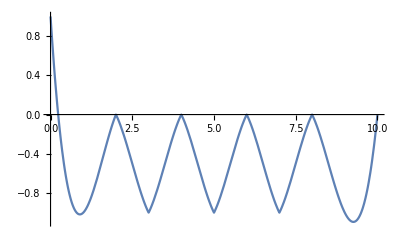

```mathematica
Plot[f[z],{z,0,10}]
```

```mathematica
Manipulate[Plot[{(-784 b+352 (-1+√(1+b))+b √(1+b) (923+4 b (-30+11 b))+a (-96 (-1+√(1+b))+b (336-393 √(1+b)+4 b √(1+b) (68+11 b))) )/(105  (3-a+10 b-6 a b)),ArcSinh[√b]/√b},{b,0.01,4.0}],{a,0.5,1.0}]
```